```mathematica
k1=-1.003664013127360 10^-2;
k2=2.194720476205664 10^+0;
k3=3.622177244599267 10^-4;
k4=4.306784511138259 10^-2;
k5=-4.712794643730906 10^+0;
k6=1.293228142971838 10^-2;
k7=-6.928742017897364 10^-1;
k8=-3.105948102428563 10^-2;
k9=3.635396623498841 10^+0;
k10=-5.577595543405037  10^-3;
```

-0.280247+0.526631 Cos[theta]-0.24361 Cos[2 theta]+0.103118 Cos[3 theta]+3.77682 Sin[theta]-5.19029 Cos[theta] Sin[theta]+0.834294 Sin[3 theta]

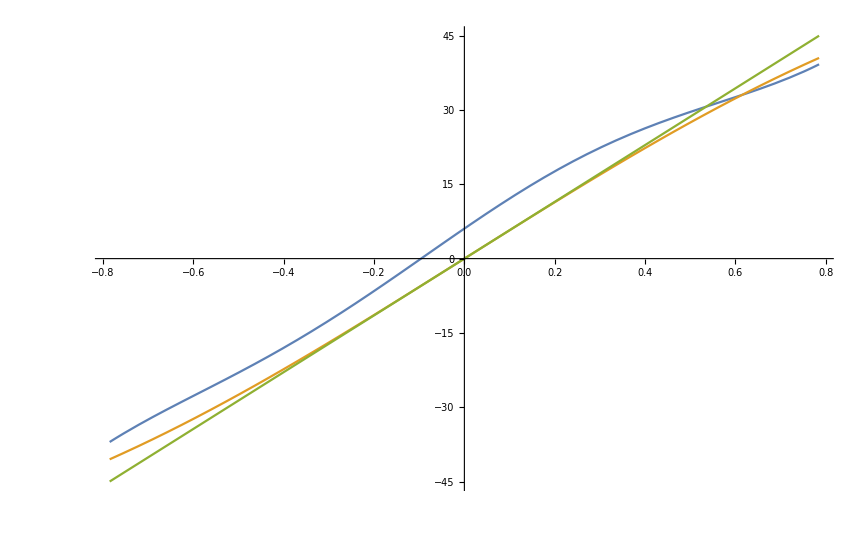

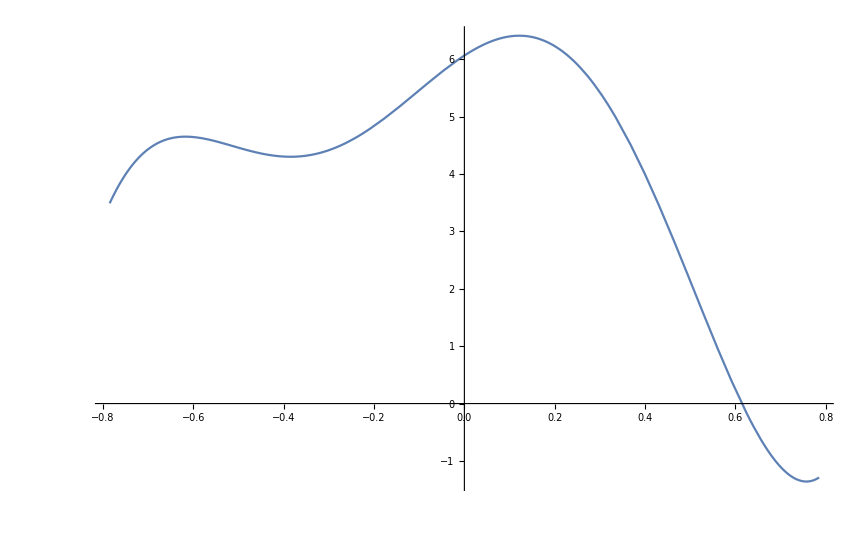

```mathematica
Y=xs Cos[theta]+(r0+ys) Sin[theta]-xd;
X=(r0+xs)Cos[theta]+ys Sin[theta]-xd;
xs=0.10;
ys=0;
xd=0.0;
r0=1;
arctg=k1 X^3+k2 X^2 Y+k3 X^2+k4 X Y^2+k5 X Y +k6 X +k7 Y^3+k8 Y^2 +k9 Y+k10;
Simplify[TrigReduce[arctg]]
Plot[{(arctg)*180/Pi,Sin[theta]*180/Pi,theta*180/Pi},{theta,-Pi/4,Pi/4}]
Plot[(arctg-Sin[theta])*180/Pi,{theta,-Pi/4,Pi/4}]
```